```mathematica
Needs["GraphUtilities`"]
```

## Substitution in algebra

This Mathematica notebook is licensed under a  
It creates the demonstrations used in the post

I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.  

This notebook contains the coding needed to produce the diagrams in the post Presenting binops as trees.  Warning : the names of many of the examples are inconsistent with each other.

### Basic definitions

```mathematica
makelabel[labs_,n_]:=Inset/@#/.labs&[n]
```

```mathematica
vertexstyle[n_]:=Framed[Style[n,FontFamily->"Arial",FontSize->12],Background->White,FrameMargins->{{3,3},{3,3}}]
```

```mathematica
vertexstyle[42]
```

42

```mathematica
edgelabelstyle[n_]:=Style[Framed[n,Background->White,FrameMargins->{{0,0},{0,0}},FrameStyle->White],Plain,FontFamily->"Arial"]
```

```mathematica
edgelabelstyle[42]
```

42

```mathematica
vrf1[labs_]:=
VertexRenderingFunction->({White,EdgeForm[Black],Black,Text[vertexstyle[makelabel[labs, #2]],#1]}&)
```

```mathematica
erf1=EdgeRenderingFunction->({Darker[Red],{Line[#1]},Text[If[#3===None,Null,edgelabelstyle[#3]],Total[#1]/2.]}&)
```

EdgeRenderingFunction→({Darker[Red],{Line[#1]},Text[If[#3===None,Null,edgelabelstyle[#3]],Total[#1]/2.]}&)

```mathematica
stree[skel_,labs_,vfr_,erf_,vcr_,imagesize_,asprat_]:=GraphPlot[skel,vfr[labs], erf,VertexCoordinateRules->vcr,EdgeLabeling->True,ImageSize->imagesize,AspectRatio ->asprat]
```

```mathematica
emptybox="  "
```

### binary operation

```mathematica
binoplabs={1->"Δ",2->"a",3->"b"}
```

{1→Δ,2→a,3→b}

```mathematica
binopskel={1->2,1->3}
```

{1→2,1→3}

```mathematica
binopvcr={1->{1,1},2->{0,0},3->{2,0}}
```

{1→{1,1},2→{0,0},3→{2,0}}

```mathematica
binop=stree[binopskel,binoplabs,vrf1,erf1,binopvcr,60,1.2]
```

-Graphics-

```mathematica
stree[binopskel,{1->"Δ",2->"a",3->"a"},vrf1,erf1,binopvcr,60,1.2]
```

-Graphics-

```mathematica
binopnovar=stree[binopskel,{1->"Δ",2->emptybox,3->emptybox},vrf1,erf1,binopvcr,60,1.3]
```

-Graphics-

```mathematica
minusnovar=stree[binopskel,{1->"minus",2->emptybox,3->emptybox},vrf1,erf1,binopvcr,60,1.3]
```

-Graphics-

```mathematica
binoponevar=stree[{1->2,1->3,2->4,3->4},{1->"Δ",2->"id",3->"id",4->emptybox},vrf1,VertexCoordinateRules->{1->{1,2},2->{0,1},3->{2,1},4->{1,0}},erf1,70,1.7]
```

-Graphics-

```mathematica
binoponevar2=stree[{1->2,1->3,2->4,3->4},{1->"Δ",2->"id",3->"id",4->"3"},vrf1,VertexCoordinateRules->{1->{1,2},2->{0,1},3->{2,1},4->{1,0}},erf1,70,1.7]
```

-Graphics-

```mathematica
binoponevar3=stree[binopskel,{1->"Δ",2->"3",3->"3"},vrf1,erf1,binopvcr,60,1.3]
```

-Graphics-

```mathematica
examplebinop2=stree[{1->2,1->3},{1->"+",2->"3",3->"5"},vrf1,erf1,binopvcr,70,1.2]
```

-Graphics-

```mathematica
examplebinop2b=stree[{1->2,1->3},{1->"+",2->"5",3->"3"},vrf1,erf1,binopvcr,70,1.2]
```

-Graphics-

```mathematica
examplebinop2evaltrace1=stree[{1->2,1->3},{1->"8",2->"3",3->"5"},vrf1,erf1,binopvcr,70,1.2]
```

-Graphics-

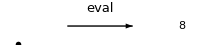

```mathematica
examplebinop2eval=Show[Graphics[{Inset[examplebinop2,{0,0}],Arrowheads[.1],Arrow[{{.3,.5},{.7,.5}}],Inset[Style["eval",13,FontFamily->"Arial"],{0.5,1}],Inset[vertexstyle[8],{1,.5}]}],ImageSize->200.00,AspectRatio->.15]
```

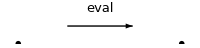

```mathematica
examplebinop2evaltrace=Show[Graphics[{Inset[examplebinop2,{0,0}],Arrowheads[.1],Arrow[{{.3,.5},{.7,.5}}],Inset[Style["eval",13,FontFamily->"Arial"],{0.5,1}],Inset[examplebinop2evaltrace1,{1,0}]}],ImageSize->200.00,AspectRatio->.15]
```

```mathematica
examplebinop3=stree[{1->2,1->3},{1->"×",2->"3",3->"5"},vrf1,erf1,binopvcr,70,1.2]
```

-Graphics-

```mathematica
examplebinop3evaltrace=stree[{1->2,1->3},{1->"15",2->"3",3->"5"},vrf1,erf1,binopvcr,70,1.2]
```

-Graphics-

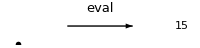

```mathematica
examplebinop3eval=Show[Graphics[{Inset[examplebinop3,{0,0}],Arrowheads[.1],Arrow[{{.3,.5},{.7,.5}}],Inset[Style["eval",13,FontFamily->"Arial"],{0.5,1}],Inset[vertexstyle[15],{1,.5}]}],ImageSize->200.00,AspectRatio->.15]
```

```mathematica
examplebinop4=stree[{1->2,1->3},{1->"minus",2->"3",3->"5"},vrf1,erf1,binopvcr,70,1.2]
```

-Graphics-

```mathematica
examplebinop4evaltrace=stree[{1->2,1->3},{1->"-2",2->"3",3->"5"},vrf1,erf1,binopvcr,70,1.2]
```

-Graphics-

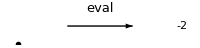

```mathematica
examplebinop4eval=Show[Graphics[{Inset[examplebinop4,{0,0}],Arrowheads[.1],Arrow[{{.3,.5},{.7,.5}}],Inset[Style["eval",13,FontFamily->"Arial"],{0.5,1}],Inset[vertexstyle[-2],{1,.5}]}],ImageSize->200.00,AspectRatio->.15]
```

```mathematica
examplelabeledbinop=stree[{{1->2,"L"},{1->3,"R"}},{1->"minus",2->"3",3->"5"},vrf1,erf1,binopvcr,90,1.2]
```

-Graphics-

```mathematica
examplebinopeval4b=stree[{1->2,1->3},{1->"minus"<>"\n"<>"-2",2->"3",3->"5"},vrf1,erf1,binopvcr,80,1.2]
```

-Graphics-

### Associative law building blocks

```mathematica
lassoc=GraphPlot[{1->2,2->3,2->4,1->5},{1->"Δ",2->"Δ",3->"a",4->"b",5->"c"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{-.67,-1},4->{.67,-1},5->{2,-1}},
ImageSize->100,AspectRatio->1]
```

-Graphics-

```mathematica
raggedlassoc=GraphPlot[{1->2,1->3,2->4,2->5},{1->"Δ",2->"Δ",3->"c",4->"a",5->"b"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{2,0},4->{-.67,-1},5->{.67,-1}},
ImageSize->100,AspectRatio->1]
```

-Graphics-

```mathematica
rassoc=GraphPlot[{1->2,1->3,2->4,2->5},{1->"Δ",2->"Δ",3->"a",4->"b",5->"c"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{1.5,0},3->{-.67,-1},4->{.67,-1},5->{2,-1}},
ImageSize->100,AspectRatio->1]
```

-Graphics-

```mathematica
minusex=GraphPlot[{1->2,1->3,2->4,2->5},{1->"minus",2->"minus",3->"c",4->"a",5->"b"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{2,0},4->{-.67,-1},5->{.67,-1}},
ImageSize->120,AspectRatio->1]
```

-Graphics-

### Evaluation

```mathematica
numinus1=GraphPlot[{1->2,1->3,2->4,2->5},{1->"minus",2->"minus",3->emptybox,4->emptybox,5->emptybox}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{2,0},4->{-.67,-1},5->{.67,-1}},
ImageSize->120,AspectRatio->1.2]
```

-Graphics-

```mathematica
numinus1r=GraphPlot[{1->2,1->3,3->4,3->5},{1->"minus",2->emptybox,3->"minus",4->emptybox,5->emptybox}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{2,0},4->{1.33,-1},5->{2.67,-1}},
ImageSize->120,AspectRatio->1.2]
```

-Graphics-

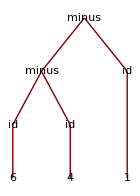

```mathematica
numinus2e0=GraphPlot[{1->2,1->3,2->4,2->5,4->6,5->7,3->8 },{1->"minus",2->"minus",3->"id",4->"id",5->"id",6->"6",7->"4",8->"1"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{2,0},4->{-.67,-1},5->{.67,-1},6->{-.67,-2},7->{.67,-2},8->{2,-2}},
ImageSize->140,AspectRatio->1.4]
```

```mathematica
numinus2e1=GraphPlot[{1->2,1->3,2->4,2->5 },{1->"minus",2->"minus",3->"1",4->"6",5->"4"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{2,0},4->{-.67,-1},5->{.67,-1}},
ImageSize->120,AspectRatio->1.2]
```

-Graphics-

```mathematica
numinus2e2=GraphPlot[{1->2,1->3 },{1->"minus",2->"2",3->"1"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{2,0}},
ImageSize->70,AspectRatio->1]
```

-Graphics-

```mathematica
numinus2e3=Show[Graphics[Inset[vertexstyle[1],{0,0}]],AspectRatio->.1]
```

-Graphics-

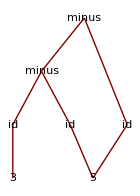

```mathematica
numinus3e0=GraphPlot[{1->2,1->3,2->4,2->5,3->7,4->6,5->7 },{1->"minus",2->"minus",3->"id",4->"id",5->"id",6->"3",7->"5"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{2,-1},4->{-.67,-1},5->{.67,-1},6->{-.67,-2},7->{1.2,-2}},
ImageSize->140,AspectRatio->1.4]
```

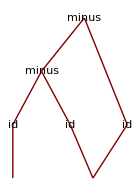

```mathematica
numinus3ebar=GraphPlot[{1->2,1->3,2->4,2->5,3->7,4->6,5->7 },{1->"minus",2->"minus",3->"id",4->"id",5->"id",6->emptybox,7->emptybox}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{2,-1},4->{-.67,-1},5->{.67,-1},6->{-.67,-2},7->{1.2,-2}},
ImageSize->140,AspectRatio->1.4]
```

```mathematica
numinus3e1=GraphPlot[{1->2,1->3,2->4,2->5 },{1->"minus",2->"minus",3->"5",4->"3",5->"5"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{2,-1},4->{-.67,-1},5->{.67,-1}},
ImageSize->120,AspectRatio->1.2]
```

-Graphics-

```mathematica
numinus3e2=GraphPlot[{1->2,1->3},{1->"minus",2->"-2",3->"5",4->"3",5->"5",6->"3",7->"5"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,-1},3->{2,-1},4->{-.67,-1},5->{.67,-1},6->{-.67,-2},7->{1.2,-2}},
ImageSize->70,AspectRatio->1.2]
```

-Graphics-

```mathematica
numinus3e3=vertexstyle[-7]
```

-7

```mathematica
examplebinop3eval=Show[Graphics[{Inset[examplebinop3,{0,0}],Arrowheads[.1],Arrow[{{.3,.5},{.7,.5}}],Inset[Style["eval",13,FontFamily->"Arial"],{0.5,1}],Inset[vertexstyle[15],{1,.5}]}],ImageSize->200.00,AspectRatio->.15]
```

```mathematica
Manipulate[Show[Graphics[{Arrowheads[.02],Inset[numinus3e0,{0,0}],Arrow[{{.45,0},{.75,0}}],
Inset[Style["eval",13,FontFamily->"Arial"],{0.6,evalheight}],
Inset[numinus3e1,{2.1 inc,0}],
Arrow[{{.4+2inc,0},{.7+2inc,0}}],
Inset[Style["eval",13,FontFamily->"Arial"],{.55+2inc,evalheight}],
Inset[numinus3e2,{3.7 inc,0}],
Arrow[{{.4+3.5 inc,0},{.7+3.5 inc,0}}],Inset[Style["eval",13,FontFamily->"Arial"],{.55+3.5 inc,evalheight}],
Inset[numinus3e3,{5.1inc,0}]}],
ImageSize->500.00,AspectRatio->Automatic],{inc,.55,2.},{evalheight,0.1,1}]
```

```mathematica
Manipulate[Show[Graphics[{Arrowheads[.02],
Inset[numinus2e1,{2.1 inc,0}],
Arrow[{{.4+2inc,0},{.7+2inc,0}}],
Inset[Style["eval",13,FontFamily->"Arial"],{.55+2inc,evalheight}],
Inset[numinus2e2,{3.7 inc,0}],
Arrow[{{.4+3.5 inc,0},{.7+3.5 inc,0}}],Inset[Style["eval",13,FontFamily->"Arial"],{.55+3.5 inc,evalheight}],
Inset[numinus2e3,{5.1inc,0}]}],
ImageSize->500.00,AspectRatio->Automatic],{inc,.55,2.},{evalheight,0.05,1}]
```

### More associative

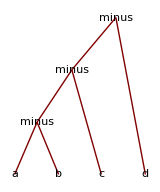

```mathematica
llassoc=GraphPlot[{1->2,1->7,2->3,2->6,3->4,3->5},{1->"minus",2->"minus",3->"minus",4->"a",5->"b",6->"c",7->"d"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{-.79,-1},4->{-1.3,-2},5->{-.3,-2},6->{.67,-2},7->{1.67,-2}},
ImageSize->160,AspectRatio->1.2]
```

```mathematica
lassoc=GraphPlot[{1->2,2->3,2->4,1->5},{1->"+",2->"+",3->"3",4->"4",5->"2"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{-.67,-1},4->{.67,-1},5->{2,-1}},
ImageSize->100,AspectRatio->1]
```

-Graphics-

### Substitution

```mathematica
binop=stree[binopskel,binoplabs,vrf1,binopvcr,60,1.2]
```

stree[{1→2,1→3},{1→Δ,2→a,3→b},vrf1,{1→{1,1},2→{0,0},3→{2,0}},60,1.2]

```mathematica
lassoc=GraphPlot[{1->2,2->3,2->4,1->5},{1->"Δ",2->"Δ",3->"a",4->"b",5->"c"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{-.67,-1},4->{.67,-1},5->{2,-1}},
ImageSize->100,AspectRatio->1]
```

-Graphics-